# Problem 2.

So this problem is just the variational technique. The way he’s writing this problem makes you believe that you need the linear variational technique (finite basis) but you can’t use that method with a single finite basis state.

Anyway, this problem should be the same (just a lot uglier) than chapter 4 - Problem 2-4

- Avocado and Mochi♥

## Part A.

Part A is the normalization constant of the wave equation.

```mathematica
Clear["Global`*"]
vo = 100;
Element[α,Reals]; (* Assume that alpha is real for this part... the normalization constant is just less ugly this way*)
ϕ[x_] = Sin[Pi*x]*Exp[-α*x];
c= 1/Sqrt[Integrate[ϕ[x]*ϕ[x],{x,0,1}]]
```

1/(π √((ⅇ^-α Sinh[α])/(2 π^2 α+2 α^3)))

I don’t really trust my solution for this because it’s so ugly, but the math is working out. Maybe it’s just like that ... I don’t judge :)

This next part is just to see the trial wave equation in the range. You can go ahead and disregard it if you’re not interested.

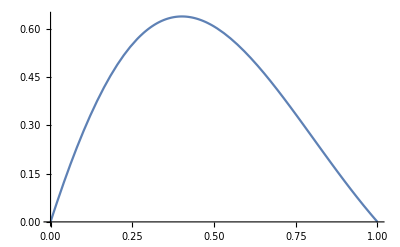

```mathematica
Plot[Sin[Pi*x] * Exp[-x],{x,0,1}]
```

This is a good trial wave equation to estimate the ground state energy within the given range.
The trial wave equation has no nodes (i.e. no zeros) within the range [0,1]. Then by the Strum’s Theorem, this wave equation will be okay for estimating ground state energy. Strum’s theorem is also known as Node Theorem (MIT open course ware) or Interlacing Theorem (Professor Mannasah).

## Part B.

Now we can begin using the Variational technique. The next four parts is the variational technique broken into steps. I guess this is his way of providing partial credit.

```mathematica
nϕ[x_] = c * Sin[Pi*x]*Exp[-α*x]; 
(* normalized wave equation *)
```

Part B is basically the kinetic energy given by the Hamiltonian.

Anyway to solve this part, you have to know that:

ψ -d/dx^2ψ = ∫ψ * -d/dx^2 ψⅆx 

Make sure to integrate in the given range. If no range is given, it’s from -∞ to ∞.

```mathematica
kineticEnergy =Integrate[nϕ[x]*(-1*D[nϕ[x],{x,2}]),{x,0,1}]
```

π^2+α^2

## Part C.

Alright so this part, is part of the potential energy given from the Hamiltonian. I guess we’re going to kind of ignore Vo for now. I think the professor is trying to check that you’re paying attention (at the end). If you’re not paying attention, you’ll end up forgetting Vo in your final answer. So be careful of that later.

The equation to solve this part is:

ψ xψ = ∫ψ * x*ψⅆx 

Integrated within the given range ([0,1] in our case). If no range is given, it will be integrated from -∞ to ∞.

```mathematica
partC = Integrate[nϕ[x]*x*nϕ[x],{x,0,1}]
potentialEnergy = Integrate[nϕ[x]*vo*x*nϕ[x],{x,0,1}];
```

1/2 (1+1/α+(2 α)/(π^2+α^2)-Coth[α])

## Part D.

Alright, so now that we have the kinetic energy and potential energy. We know that the energy as a function of α is the linear combination of those two. From General Physics 1 we know that Energy = Kinetic Energy + Potential Energy 

Basically we’re going to follow the law of conservation of energy. Except all these energies are a function of α.

```mathematica
energy = kineticEnergy + potentialEnergy
```

π^2+α^2+50 (1+1/α+(2 α)/(π^2+α^2)-Coth[α])

Now we know from Calculus I, to find the maxima or minima (extrema) of a function, we have to take the derivative of the function. Then find when this derivative is equal to 0. 

Basically this is a turning point of a given function - this turning point is a local extrema.

```mathematica
denergy = D[energy,{α,1}]
```

2 α+50 (-1/α^2-(4 α^2)/((π^2+α^2)^2)+2/(π^2+α^2)+Csch[α]^2)

```mathematica
Solve[denergy == 0, α]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[2 α+50 (-1/α^2-(4 α^2)/((π^2+α^2)^2)+2/(π^2+α^2)+Csch[α]^2)==0,α]

Alright it looks like Mathematica can solve this problem!

Oh no! I guess it’s time to give up!

Nah, it’s not. We just have to think outside the box a little. We’re engineers right ? :)

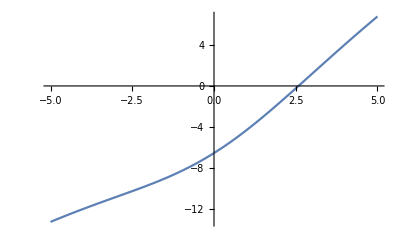

```mathematica
Plot[denergy==0,{α,-5,5}]
```

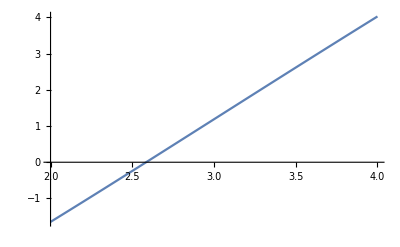

```mathematica
Plot[denergy==0,{α,2,4}]
```

Would you look at that! 

Now we can use FindRoot to find our zero instead :)

```mathematica
FindRoot[denergy ==0 , {α,2.6}]
```

{α→2.5847}

There we go, an α value!

```mathematica
α=2.5847027304579955;
groundStateEnergy = energy
```

50.9401